## Parameter Planes

## Import data and Settings

```mathematica
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/export_data/temp_anomaly"];
```

```mathematica
(* Heat data for delta and kappa variation (different bin sizes) *)
```

```mathematica
kappaDeltaProj0=Import["heat_delta_kappa_proj0.dat"];
kappaDeltaProj25=Import["heat_delta_kappa_proj25.dat"];
kappaDeltaProj50=Import["heat_delta_kappa_proj50.dat"];
kappaDeltaProj100=Import["heat_delta_kappa_proj100.dat"];
```

### Settings

```mathematica
imgs=200;
```

## Changing temperature projection

```mathematica
colScheme="LightTemperatureMap";
(*colScheme="TemperatureMap";*)
(*colScheme={"BeachColors","Reverse"};*)
(*colScheme={"SolarColors","Reverse"};*)
(*colScheme2=(Blend[{TMBcolours[[1]],TMBcolours[[2]],TMBcolours[[4]]},#]&);*)
```

```mathematica
(* create a color legend that spans range of temperatures *)
tempRange={1.2,5.5};
colLegend=BarLegend[{colScheme,tempRange},LegendLabel->"T (°C)",LegendMarkerSize->150]
```

```mathematica
(* Rescale temperatures so that temperature range is mapped to (0,1) *)
kappaDeltaProj0[[;;,3]]=Rescale[kappaDeltaProj0[[;;,3]],tempRange,{0,1}];
kappaDeltaProj25[[;;,3]]=Rescale[kappaDeltaProj25[[;;,3]],tempRange,{0,1}];
kappaDeltaProj50[[;;,3]]=Rescale[kappaDeltaProj50[[;;,3]],tempRange,{0,1}];
kappaDeltaProj100[[;;,3]]=Rescale[kappaDeltaProj100[[;;,3]],tempRange,{0,1}];
```

```mathematica
ColorFunction->(Blend[{Lighter[Yellow,.8],Orange,Red},#3]&)
```

ColorFunction→(Blend[{Lighter[Yellow,0.8],Orange,Red},#3]&)

```mathematica
(* temperature projection 0 yrs *)
heatMapProj0=ListDensityPlot[kappaDeltaProj0,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->colScheme,
FrameLabel->{"κ","δ"},LabelStyle->14,ImageSize->imgs
];
```

```mathematica
(* temperature projection 25 yrs *)
heatMapProj25=ListDensityPlot[kappaDeltaProj25,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->colScheme,
FrameLabel->{"κ","δ"},LabelStyle->14,ImageSize->imgs
];
```

```mathematica
(* temperature projection 50 yrs *)
heatMapProj50=ListDensityPlot[kappaDeltaProj50,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->colScheme,
FrameLabel->{"κ","δ"},LabelStyle->14,ImageSize->imgs
];
```

```mathematica
(* temperature projection 100 yrs *)
heatMapProj100=ListDensityPlot[kappaDeltaProj100,
InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->colScheme,
FrameLabel->{"κ","δ"},LabelStyle->14,ImageSize->imgs
];
```

### Graphics Row

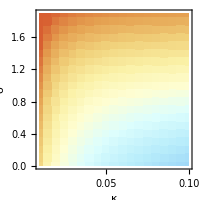
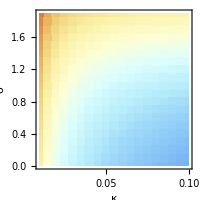
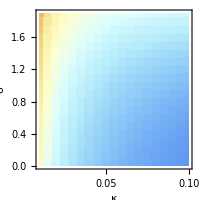
-Graphics- | -Graphics- | -Graphics- |

```mathematica
planesTempproj=Grid[{{heatMapProj0,heatMapProj25,heatMapProj50,colLegend}}]
```

```mathematica
(*Export["../../figures/planesTempproj.png",planesTempproj,ImageResolution->200];*)
```